```mathematica
machineZero = 10^(-$MachinePrecision);
<<MaTeX`
```

## N - functions

The following are the necessary N functions for the 5D RGE’s (N_(++), N_(+-), N_(-+),N_(--) (μ, {P_ξ}) ) where {P_ξ} = {s_ξ, r0_ξ, rπ_ξ, α}, where:
		 s_ξ = {2, 4, 1, 1}                               for                      ξ∈{Aμ, ϕ, exp(-2k L5 |y|) ψL, exp(-2k L5 |y|) ψR }	;
		 α = Sqrt [   (sξ/2)^2 + M_ξ^2 ]           where         M_ξ^2 ∈  { 0, 0, c(c+1), c(c-1) }

```mathematica
(* N_(++) *)
Npp[μ_,sξ_, r0ξ_, rπξ_, αξ_]:= Module[ {μAux},
Return[
(( sξ/2 - r0ξ ) BesselJ[αξ, μ / k ]  + μ/k D[BesselJ[αξ, μAux], μAux]/.{μAux->μ/k}) * (  ( sξ/2 - rπξ ) BesselY[αξ, μ / (k zL) ]  + μ/(k zL) D[BesselY[αξ, μAux], μAux]/.{μAux->μ/(k zL)}) +(  ( sξ/2 - rπξ ) BesselJ[αξ, μ / (k zL) ]  + μ/(k zL) D[BesselJ[αξ, μAux], μAux]/.{μAux->μ/(k zL)}) *(  ( sξ/2 - r0ξ ) BesselY[αξ, μ / k ]  + μ/k D[BesselY[αξ, μAux], μAux]/.{μAux->μ/k}) ];
];

(*N_(+-)*)
Npm[μ_,sξ_, r0ξ_, rπξ_, αξ_]:= Module[{μAux},
Return[
-  BesselY[αξ, μ / (k zL) ] *(  ( sξ/2 - r0ξ ) BesselJ[αξ, μ / k ]  + μ/k D[BesselJ[αξ, μAux], μAux]/.{μAux->μ/k})  +  BesselJ[αξ, μ / (k zL) ] * (  ( sξ/2 - r0ξ ) BesselY[αξ, μ / k ]  + μ/k D[BesselY[αξ, μAux], μAux]/.{μAux->μ/k})];
];

(*N_(-+)*)
Nmp[μ_,sξ_, r0ξ_, rπξ_, αξ_]:= Module[{μAux},
Return[
BesselJ[αξ, μ / k ] * (  ( sξ/2 - rπξ ) BesselY[αξ, μ / (k zL) ]  + μ/(k zL) D[BesselY[αξ, μAux], μAux]/.{μAux->μ/(k zL)})  - 
 BesselY[αξ, μ / k ]*(  ( sξ/2 - rπξ ) BesselJ[αξ, μ / (k zL) ]  + μ/(k zL) D[BesselJ[αξ, μAux], μAux]/.{μAux->μ/(k zL)}) ];
];


(*N_(--)*)
Nmm[μ_,sξ_, r0ξ_, rπξ_, αξ_]:= Module[{μAux},
Return[
BesselJ[αξ, μ / k ] * BesselY[αξ, μ / (k zL) ]  - BesselJ[αξ, μ / (k zL) ]  * BesselY[αξ, μ / k ]
 ];
];

(*N functions that take into account the ±± assignment and the field type to assign the right r0, rπ, α, s, *)
NForξ[μVar_, ξType_, Mξ_, sign1_, sign2_]:=Module[
{sξ, αξ, r0ξ, rπξ},

If[ξType=="Boson",
If[sign1==1 && sign2==1,
sξ=4;αξ=0;r0ξ = rπξ=2;
Return[Nmm[μVar, sξ, r0ξ, rπξ, αξ]];
,
sξ=2;αξ= 1;r0ξ = rπξ=0;]

,
If[ξType == "FermionL",
If[sign1==1 && sign2==1,
sξ=1;r0ξ = rπξ=Mξ;αξ = Abs[Mξ-1/2];
Return[Nmm[μVar, sξ, r0ξ, rπξ, αξ]];
,
sξ=1;r0ξ = rπξ=-Mξ;αξ= Abs[Mξ+1/2];]

,
If[ξType == "FermionR",
If[sign1==1 && sign2==1,
sξ=1;r0ξ = rπξ=-Mξ;αξ = Abs[Mξ+1/2];
Return[Nmm[μVar, sξ, r0ξ, rπξ, αξ]];
,
sξ=1;r0ξ = rπξ=Mξ;αξ= Abs[Mξ-1/2];]

,
If[ξType == "Scalar",
sξ=4;r0ξ = rπξ=0;αξ= 2;
If[sign1==1 && sign2==1,
Return[Npp[μVar, sξ, r0ξ, rπξ, αξ]];  ]]
]]];


If[sign1==1 && sign2==-1,
Return[Npm[μVar, sξ, r0ξ, rπξ, αξ]];
,
If[sign1==-1 && sign2==1,
Return[Nmp[μVar, sξ, r0ξ, rπξ, αξ]];
,
If[ sign1 == -1 && sign2 == -1,
Return[Nmm[μVar, sξ, r0ξ, rπξ, αξ]];
]]];
];
```

## SU(N) :: T_a Dynkin indices and Casimirs.

This bit of code should in principle deliver the Dynkin index and/or Casimir (is the same for the adjoint) given the SU(N) algebra and it’s dimension.

E.g. say we have SU(4) so N = 4, and we want the Dynkin index of 15, 4, and 6  representations. The code will go through the steps based on hep-ph/1511.08771:

	1) Check what su_n irrep the dimension of the representation, d(R) against all the possible irreps , it corresponds to :
		E.g. For 4 ,  d(4) = 4 = n    ∴   the su_4 irrep is (100)  (if it was \bar{4}   then it would have been it’s conjugate (001) )
		E.g For 6 ,   d(6) = 6 = (4* (4-1))/2  
		
	2) Once we’ve identified which irrep we’re working with we simply return it’s Dynkin Index T(R) or Casimir C_2(R) if prompted by the 	user. Corresponding to the equations:
	
		T(R) = d(R)/ d(G)  * C_2 (R) 			                  - where d(G) = dimension of the adjoint, C_2 (R) quadratic Casimir given by:
		 C_2 (R) = 1/2 Σ_(i, j =1 → n)(ai + 2 gi ) G(su_(n+1))ij aj	        - for a irrep (a1 a2 ... an) where G(su_(n+1)) is the inverse Cartan matrix(also known as the metric matrix)
		 
	We’ll just go and use their results on a comparison basis from Table 20.

```mathematica
makeSUNassocDict[n_]:=Module[
{dRDict, casKey, dynKey, descKey},
casKey = "QuadCasimir";
dynKey = "DynkinIdx";
descKey ="IrrepDesc";



dRDict = <| "1"-> <|casKey->0 ,  dynKey-> 1/2, descKey->"Scalar Irrep (0000...0000)"|> |>;

If[n≥2,
AppendTo[dRDict,ToString[n]-><|casKey->(n^2 - 1)/2n ,   dynKey-> 1/2, descKey->"Fundamental Irrep (1000...0000)"|>];

AppendTo[dRDict,ToString[n * (n+1)/2] ->   <|casKey -> (n-1)(n+2)/2, dynKey-> (n+2)/2, 
descKey->"Irrep (2000...0000)"|>];

AppendTo[dRDict,ToString[n^2 - 1]->             <|casKey -> n, dynKey-> n,
descKey->"Adjoint Irrep (1000...0001)"|>];


];

If[n≥3,
AppendTo[dRDict, ToString[n * (n-1)/2] ->   <|casKey->(n+1)(n-2)/n ,  dynKey-> (n-2)/2, descKey->"Irrep (0100...0000)"|>];
];
If[n≥5,
AppendTo[dRDict,ToString[n * (n-1)(n-2)/6] ->   <|casKey -> (n-2)(n-3)(n-4)/12, dynKey-> (n-3)(n-2)/4, descKey->"Irrep (0010...0000)"|>];
AppendTo[dRDict,ToString[n * (n-1)(n+1)/3] ->   <|casKey -> 3(n^2-3)/(2n), dynKey-> (n^2-3)/2, descKey->"Irrep (1100...0000)"|>];
AppendTo[dRDict,ToString[n * (n+1)(n+2)/6] ->   <|casKey -> (n+2)(n+3)(n+4)/12, dynKey-> (n+2)(n+3)/4, descKey->"Irrep (3000...0000)"|>];
AppendTo[dRDict,ToString[n^2 * (n+1)(n-1)/12] ->   <|casKey -> n(n^2 - 16)/3, dynKey-> n(n-2)(n+2)/6, descKey->"Irrep (0200...0000)"|>];
];


Return[dRDict]
];
```

## Δ_a - 1 loop corrections - GeneralForm

The expressions for the 5D RGE’s corrections Δ_a (ξ, μ) as layed  out in hep-th/0208071v3

```mathematica
makeDeltaForSUNscalar[n_, sign1_, sign2_, μ_, Mξ_, dR_, ΛCutoff_]:=Module[
{Nfunc, Δaϕ, irrepDictSUN, Taϕ, Nvar,  nIntFct, numIntRes, u},



(* Performing the N function numerical integration *)
(* NOTE! You should only keep the real part of the integration for (-,-) since the imaginary part is super oscillatory and should be 0 in the theory. All other cases have Im = 0 See commented plotting code for clarification  *)
Nvar = (ⅈ u)/2* Sqrt[μ^2];


Nfunc = NForξ[Nvar, "Scalar", Mξ, sign1, sign2];
nIntFct = u(1-u^2)^(1/2)* Log[Nfunc];
(*numIntRes = NIntegrate[Re @ nIntFct,{u, 0.0, 1.0}];*)


numIntRes =Quiet[ NIntegrate[Re @ nIntFct,{u, machineZero, 1.0}]];
(*Plot[{
Re @ N[Log[NForξ[ⅈ x, "Scalar",0,pm1, pm2]/.{x->50*uval}]] * uval(1-uval^2)^(1/2),
Im @ N[Log[NForξ[ⅈ x, "Scalar",0, pm1, pm2]/.{x->50*uval}]] * uval(1-uval^2)^(1/2)},
{uval, 0.0, 1.0}, PlotLegends->{"Real", "Imaginary"}]*)


(*Make the gauge structure dictionary*)
irrepDictSUN = makeSUNassocDict[n];
Taϕ = irrepDictSUN[[ ToString[dR] ]][["DynkinIdx"]];

(*Construct and return the Δ corrections*)
If[sign1==1 && sign2==1,
Δaϕ = 1/12 * Taϕ * (Log[ΛCutoff/k] -  3*numIntRes  )  ;
,
If[(sign1 ==1 && sign2 == -1) || (sign1 == -1 && sign2 == +1),
Δaϕ = 1/12*((-3)* Taϕ * numIntRes);
,
If[sign1 == -1 && sign2 == -1,
Δaϕ = -1/12 * Taϕ * (Log[ΛCutoff/k] +  3*numIntRes  )  ;

]]];


Return[Δaϕ];]

(******************  Fermions  *********************)

makeDeltaForSUNFermion[n_, sign1_, sign2_, μ_, Mξ_, dR_, L5_, FermionStr_]:=Module[
{Nfunc, Δaψ, irrepDictSUN, Taψ, Nvar, u, nIntFct, numIntRes},


(* Performing the N function numerical integration *)
Nvar = (ⅈ u)/2* Sqrt[μ^2];

If[sign1==1 && sign2 ==1 &&  FermionStr =="FermionL",Nfunc = NForξ[Nvar, "FermionR", Mξ, sign1, sign2];,

If[sign1==1 && sign2 ==1 &&  FermionStr =="FermionR", Nfunc = NForξ[Nvar, "FermionL", Mξ, sign1, sign2];,
Nfunc = NForξ[Nvar, FermionStr, Mξ, sign1, sign2];

]];



nIntFct =(  u(1-u^2)^(1/2) - u(1-u^2)^(-1/2) )* Log[Nfunc];
numIntRes =Quiet[ NIntegrate[Re @ nIntFct,{u, machineZero, 1.0}]];

(*Make the gauge structure dictionary*)
irrepDictSUN = makeSUNassocDict[n];
Taψ = irrepDictSUN[[ ToString[dR] ]][["DynkinIdx"]];


If[ (sign1 ==1 && sign2 == 1) || (sign1 == -1 && sign2 == -1),
Δaψ = 1/3 * Taψ * (2 Log[k/μ ] -k L5 +  3*numIntRes  ) ;
,

If[sign1 ==1 && sign2 == -1,
Δaψ = 1/3 * Taψ *(-k L5 + 3 numIntRes);
,

If[sign1==-1&& sign2==1,
Δaψ = 1/3 * Taψ * (k L5 + 3 numIntRes);]]];

Return[Δaψ];];


(******************  Vector bosons  *********************)
makeDeltaForSUNVector[n_, sign1_, sign2_, μ_, Mξ_, dR_, L5_, Λ_]:=Module[
{Nfunc, ΔaA, irrepDictSUN, TaA, Nvar, u, nIntFct, numIntRes},


(* Performing the N function numerical integration *)
Nvar = (ⅈ u)/2* Sqrt[μ^2];
Nfunc = NForξ[Nvar, "Boson", Mξ, sign1, sign2];
nIntFct = (  -9 u(1-u^2)^(1/2) +24 u(1-u^2)^(-1/2) )* Log[Nfunc];
numIntRes =Quiet[ NIntegrate[Re @ nIntFct,{u,machineZero, 1.0}]];

(*Make the gauge structure dictionary*)
irrepDictSUN = makeSUNassocDict[n];
TaA = irrepDictSUN[[ ToString[dR] ]][["DynkinIdx"]];


If[ sign1 ==1 && sign2 ==1,
ΔaA = 1/12*TaA*(23 Log[μ/ Λ] + 21 Log[μ /k] + 22 k L5 + numIntRes);
,

If[ sign1 == +1 && sign2 == -1,
ΔaA = 1/12* TaA * (-k L5 + numIntRes);
,

If[sign1 == -1 && sign2 == +1,
ΔaA =1/12* TaA * (k L5 + numIntRes);
,

If[ sign1 == -1 && sign2 == -1,
ΔaA = 1/12*TaA*(23 Log[μ/ Λ] + 2Log[μ /k] - k L5 + numIntRes);
]


]]];
Return[ΔaA];
];
```

## 5D 1Loop corrections for GHGUT approximation

```mathematica
(*n_, sign1_, sign2_, μ_, Mξ_, dR_, ΛCutoff_*)
```

```mathematica
(*Clear[]*)
SU4Corr[μVal_, ΛCut_, L5_, c0_, c0Prime_, c1_, c2_]:=Module[
{nbOfQuarkGens, SUN, SU4ScalarCorr, SU4FermionCorr, SU4VectorCorr, fullSU4Corr},

SUN=4;

(* Scalar contribution*)
SU4ScalarCorr = 2*makeDeltaForSUNscalar[SUN,-1, -1,μVal, 0, 15, ΛCut];

(*Fermion Contributions*)
nbOfQuarkGens = 3;

SU4FermionCorr = nbOfQuarkGens*(makeDeltaForSUNFermion[SUN, +1, +1, μVal, c0, 4,L5, "FermionL"]+
makeDeltaForSUNFermion[SUN, +1, +1, μVal, c0, 4,L5, "FermionR"] + 
makeDeltaForSUNFermion[SUN, -1, -1, μVal, c0, 4,L5, "FermionL"] + 
makeDeltaForSUNFermion[SUN, -1, -1, μVal, c0, 4,L5, "FermionR"]) + 
nbOfQuarkGens*(makeDeltaForSUNFermion[SUN, +1, +1, μVal, c1, 6,L5, "FermionL"] + 
makeDeltaForSUNFermion[SUN, +1, +1, μVal, c1, 6,L5, "FermionR"] + 
makeDeltaForSUNFermion[SUN, -1, -1, μVal, c1, 6,L5, "FermionL"] + 
makeDeltaForSUNFermion[SUN, -1, -1, μVal, c1, 6,L5, "FermionR"]) +
makeDeltaForSUNFermion[SUN, +1, -1, μVal, c0Prime, 4,L5, "FermionL"] + makeDeltaForSUNFermion[SUN, -1, +1, μVal, c0Prime, 4,L5, "FermionR"] + makeDeltaForSUNFermion[SUN, -1, +1, μVal, c0Prime, 4,L5, "FermionL"] + makeDeltaForSUNFermion[SUN, +1, -1, μVal, c0Prime, 4,L5, "FermionR"];

(*Note that 3bar is identical to 3 when our concern is RGE runnings since it only depends on the Dynkin index which is the same*)
SU4VectorCorr = makeDeltaForSUNVector[SUN-1, +1, +1, μVal, 0, 8,L5, ΛCut] +
makeDeltaForSUNVector[SUN-1, -1, +1, μVal, 0, 3,L5, ΛCut]+ 
makeDeltaForSUNVector[SUN-1, -1, +1, μVal, 0, 3,L5, ΛCut];

fullSU4Corr = SU4ScalarCorr + SU4FermionCorr + SU4VectorCorr;
Return[1/(8 π^2)fullSU4Corr];
]

SU2LCorr[μVal_, ΛCut_, L5_, c0_, c0Prime_, c1_, c2_]:=Module[
{nbOfQuarkGens, SUN, SU2LScalarCorr, SU2LFermionCorr, SU2LVectorCorr, fullSU2LCorr},

SUN=2;

(* Scalar contribution*)
SU2LScalarCorr = makeDeltaForSUNscalar[SUN,+1, +1,μVal, 0, 2, ΛCut] + 2* makeDeltaForSUNscalar[SUN,-1, -1,μVal, 0, 3, ΛCut] ;

(*Fermion Contributions*)
nbOfQuarkGens = 3;
SU2LFermionCorr = nbOfQuarkGens*(makeDeltaForSUNFermion[SUN, +1, +1, μVal, c0, 2,L5, "FermionL"] + 
makeDeltaForSUNFermion[SUN, -1, -1, μVal, c0, 2,L5, "FermionR"]) + 
nbOfQuarkGens *(makeDeltaForSUNFermion[SUN, +1, +1, μVal, c2, 2,L5, "FermionL"]+ 
			 makeDeltaForSUNFermion[SUN, +1, +1, μVal, c2, 2,L5, "FermionR"]+
			 makeDeltaForSUNFermion[SUN, -1, -1, μVal, c2, 2,L5, "FermionL"] +
			 makeDeltaForSUNFermion[SUN, -1, -1, μVal, c2, 2,L5, "FermionR"]
)+
	makeDeltaForSUNFermion[SUN, +1, -1, μVal, c0Prime, 2,L5, "FermionL"] + makeDeltaForSUNFermion[SUN, -1, +1, μVal, c0Prime, 2,L5, "FermionR"];

SU2LVectorCorr = makeDeltaForSUNVector[SUN, +1, +1, μVal, 0, 3,L5, ΛCut] +
			      makeDeltaForSUNVector[SUN, -1, -1, μVal, 0, 2,L5, ΛCut] 
;

fullSU2LCorr = SU2LScalarCorr + SU2LFermionCorr + SU2LVectorCorr;
Return[1/(8π^2) fullSU2LCorr];

]


SU2RCorr[μVal_, ΛCut_, L5_, c0_, c0Prime_, c1_, c2_]:=Module[
{nbOfQuarkGens, SUN, SU2RScalarCorr, SU2RFermionCorr, SU2RVectorCorr, fullSU2RCorr},

SUN=2;

(* Scalar contribution*)
SU2RScalarCorr = makeDeltaForSUNscalar[SUN,+1, +1,μVal, 0, 2, ΛCut] + 2* makeDeltaForSUNscalar[SUN,-1, -1,μVal, 0, 3, ΛCut] ;

(*Fermion Contributions*)
nbOfQuarkGens = 3;
SU2RFermionCorr = nbOfQuarkGens*(makeDeltaForSUNFermion[SUN, +1, +1, μVal, c0, 2,L5, "FermionL"] + 
makeDeltaForSUNFermion[SUN, -1, -1, μVal, c0, 2,L5, "FermionR"]) + 
nbOfQuarkGens *(makeDeltaForSUNFermion[SUN, +1, +1, μVal, c2, 2,L5, "FermionL"]+ 
			 makeDeltaForSUNFermion[SUN, +1, +1, μVal, c2, 2,L5, "FermionR"]+
			 makeDeltaForSUNFermion[SUN, -1, -1, μVal, c2, 2,L5, "FermionL"] +
			 makeDeltaForSUNFermion[SUN, -1, -1, μVal, c2, 2,L5, "FermionR"]
)+
	makeDeltaForSUNFermion[SUN, -1, +1, μVal, c0Prime, 2,L5, "FermionL"] +  
         makeDeltaForSUNFermion[SUN, +1, -1, μVal, c0Prime, 2,L5, "FermionR"];

SU2RVectorCorr = makeDeltaForSUNVector[SUN, -1, +1, μVal, 0, 3,L5, ΛCut] +
			      makeDeltaForSUNVector[SUN, -1, -1, μVal, 0, 2,L5, ΛCut] 
;

fullSU2RCorr = SU2RScalarCorr + SU2RFermionCorr + SU2RVectorCorr;
Return[1/(8π^2) fullSU2RCorr];

]
```

## Main call

Recall α = g^2 / (4 π).

```mathematica
k= 89000;                             
zL =35; 
mKK5 = (π k)/(zL -1);
c0 =0.3325; 
c1 =0.0;
c2 =-0.7;
c0Prime =0.5224;

L5 = N[Log[zL]/(k)];
Λ = 10^13;
(*sAμ = 2;
r0=rπ = 0;
α = Sqrt[(sAμ / 2)^2]*)
(*Clear[k, zL, sAμ, r0, rπ, α]*)


MZ = 80;
(*Clear[Λ]*)
(*Λ = 10^5;*)

SUN = 4;
pm1 = +1;
pm2 = +1;


gSU2R= Sqrt[4 π /55];
gSU4= Sqrt[4 π /30];
(*Determining ΛMax for diferent couplings via the functional route.*)
(* Uncomment bellow for simple approximation *)
(*CtSU4Approx =π/(2 gSU4) /.{μMain-> mKK5};ΛMaxApprox = CtSU4Approx * 16 π  / L5;*)


CSU2RSol  = FindRoot[1/gSU2R^2 -SU2RCorr[mKK5, ΛFake, L5, c0, c0Prime, c1, c2] - CSU2R/.{ΛFake-> 16 π / L5 * CSU2R}, {CSU2R, 100}];
ΛMaxFunctional2R = CSU2R * 16 π  / L5 /.CSU2RSol


CtSU4Approx =π/(2 gSU4) /.{μMain-> mKK5};
ΛMaxApprox = CtSU4Approx * 16 π  / L5;
```

5.92123×10^6

Functional route ΛMax : 1.95251×10^6
 Approximation route for ΛMax : 3.05389×10^6

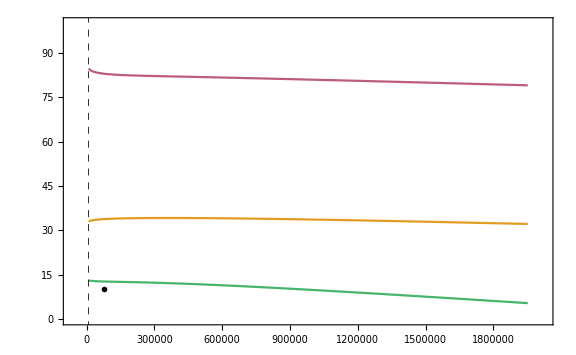

```mathematica
(*Inital values for Couplings*)
α4inv =13 + 1/(12 π);
α2Linv = 33;
α2Rinv = 5/3(56-2/5(α4inv - 1/(3 π))) + 1/(6 π);

Print[]
gSU4= Sqrt[4 π /α4inv];
gSU2L= Sqrt[4 π /α2Linv];
gSU2R= Sqrt[4 π /α2Rinv];

(*Determining ΛMax for diferent couplings via the functional route.*)
(* Uncomment bellow for simple approximation *)
(*CtSU4Approx =π/(2 gSU4) /.{μMain-> mKK5};ΛMaxApprox = CtSU4Approx * 16 π  / L5;*)


CSU2RSol  = FindRoot[1/gSU2R^2 -SU2RCorr[mKK5, ΛFake, L5, c0, c0Prime, c1, c2] - CSU2R/.{ΛFake-> 16 π / L5 * CSU2R}, {CSU2R, 100}];
ΛMaxFunctional2R = CSU2R * 16 π  / L5 /.CSU2RSol;
CSU2LSol  = FindRoot[1/gSU2L^2 -SU2LCorr[mKK5, ΛFake, L5, c0, c0Prime, c1, c2] - CSU2L/.{ΛFake-> 16 π / L5 * CSU2L}, {CSU2L, 100}];
ΛMaxFunctional2L = CSU2L * 16 π  / L5 /.CSU2LSol;
CSU4Sol  = FindRoot[1/gSU4^2 -SU4Corr[mKK5, ΛFake, L5, c0, c0Prime, c1, c2] - CSU4/.{ΛFake-> 16 π / L5 * CSU4}, {CSU4, 100}];
ΛMaxFunctional = CSU4 * 16 π  / L5 /.CSU4Sol;



Print["Functional route ΛMax : ", ΛMaxFunctional , 
	"\n Approximation route for ΛMax : ", ΛMaxApprox];


texStyle={FontFamily->"Latin Modern Roman", FontSize ->13};
ΛMaxPlot = Min[ΛMaxFunctional, ΛMaxFunctional2L, ΛMaxFunctional2R];


plot=Plot[
	    {
	 4π(CSU4  + SU4Corr[μPlot, ΛMaxFunctional, L5, c0, c0Prime, c1, c2]/. CSU4Sol),
	    4π(CSU2L  + SU2LCorr[μPlot, ΛMaxFunctional2L, L5, c0, c0Prime, c1, c2]/. CSU2LSol),
	    4π(CSU2R  + SU2RCorr[μPlot, ΛMaxFunctional2R, L5, c0, c0Prime, c1, c2]/. CSU2RSol)
},
 
	{μPlot,mKK5, ΛMaxPlot},

	Frame->True,FrameStyle->BlackFrame,
	FrameLabel->MaTeX[{"\\mu (GeV)"," \\alpha^{-1}"}, FontSize->24],
	BaseStyle->texStyle, 
	ImageSize->Large,
	Epilog->{Dashed,Thickness[0.001], { InfiniteLine[{{mKK5,0.0},{mKK5,0.5}}]},
	
       		Inset[MaTeX["m_{\\text{KK}_5}",Magnification->1.4],{mKK5+0.7*10^5, 10},Scaled[{0.5,1}]]},
	PlotRange->{{mKK5-0.7*10^5, ΛMaxPlot+0.7*10^5},{0, 100}},

	PlotLegends->MaTeX[{"\\frac{4\\pi}{g^2_{4C}}", "\\frac{4\\pi}{g^2_{2L}}",  "\\frac{4\\pi}{g^2_{2R}}"}, FontSize->18],
	PerformanceGoal->"Speed",
	PlotStyle->{ColorData[97,"ColorList"][[15]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[14]]}
]
```

```mathematica
α2LinvatLambda = N[4π(CSU2L  + SU2LCorr[ΛMaxPlot, ΛMaxFunctional2L, L5, c0, c0Prime, c1, c2]/. CSU2LSol)];
α2RinvatLambda =N[4π(CSU2R  + SU2RCorr[ΛMaxPlot, ΛMaxFunctional2R, L5, c0, c0Prime, c1, c2]/. CSU2RSol)];
α4CinvatLambda= N[4π(CSU4  +  SU4Corr[ΛMaxPlot, ΛMaxFunctional, L5, c0, c0Prime, c1, c2]/. CSU4Sol)];
```

```mathematica
α2LWeinb = 1/ α2LinvatLambda;
α2RWeinb = 1/ α2RinvatLambda;
α4CWeinb = 1/ α4CinvatLambda;
CassDiff = 1/(12 π)(3/5*2+2/5* 4);
sin2ThWEvolved = ((α2LWeinb α4CWeinb+ 2/3 α2LWeinb α2RWeinb + α2RWeinb α4CWeinb - 5/3 α2LWeinb α2RWeinb α4CWeinb*CassDiff)/(α2RWeinb α4CWeinb))^(-1);
Print["@ΛMax, have evolved value of sin^2 θW :", sin2ThWEvolved];
```

@ΛMax, have evolved value of sin^2 θW :0.280375

```mathematica
N[Log10[mKK5]]
```

3.91506

-Graphics-

{-Graphics-,-Graphics-,-Graphics-}

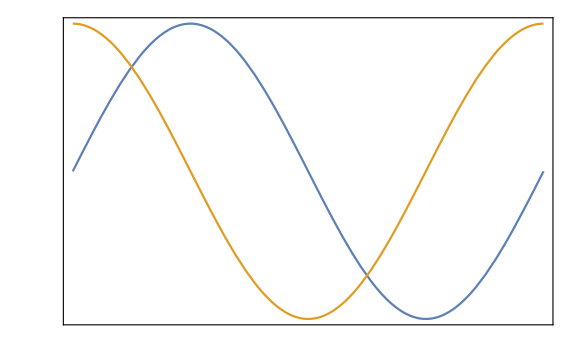

```mathematica
(*Display in LaTeX*)
MaTeX@ HoldForm[Sum[1/n!, {n=1, ∞}]]
MaTeX[{"\\frac{x^2}{\\sqrt{3}}",HoldForm[Integrate[Sin[x],{x,0,2 Pi}]],Expand[(1+x)^5]}, FontSize->18]
myRange = {0, π/2, π, π/4, -π/4, -π/2  };


Plot[{Sin[x], Cos[x]},{x,0,2 Pi},
Frame->True,FrameStyle->BlackFrame,
FrameTicks->{{Table[{Sin[x], MaTeX[Sin[x], FontSize->18]}, {x, myRange}],None},
		      {Table[{x,MaTeX[x,"DisplayStyle"->False, FontSize->18]},{x,Pi/4 Range[0,8]}],None}},
FrameLabel->MaTeX[{"x","\\sin x"}, FontSize->24],
BaseStyle->texStyle, 
ImageSize->Large,

(*Epilog->{Inset[MaTeX["x^2+y^4=1",Magnification->2],{3.0, 0.0},Scaled[{0.5,1}]]},*)
PlotLegends->MaTeX[{"\\sin x","\\cos x"}, FontSize->18]
]
```

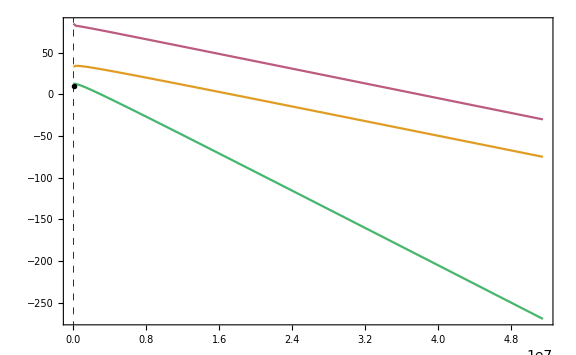

```mathematica
ΛMaxPlot = 5.147762002327099*^7;
plot=Plot[
	    {
	 4π(CSU4  + SU4Corr[μPlot, ΛMaxFunctional, L5, c0, c0Prime, c1, c2]/. CSU4Sol),
	    4π(CSU2L  + SU2LCorr[μPlot, ΛMaxFunctional2L, L5, c0, c0Prime, c1, c2]/. CSU2LSol),
	    4π(CSU2R  + SU2RCorr[μPlot, ΛMaxFunctional2R, L5, c0, c0Prime, c1, c2]/. CSU2RSol)
},
 
	{μPlot,mKK5, ΛMaxPlot},

	Frame->True,FrameStyle->BlackFrame,
	FrameLabel->MaTeX[{"\\mu (GeV)"," \\alpha^{-1}"}, FontSize->24],
	BaseStyle->texStyle, 
	ImageSize->Large,
	Epilog->{Dashed,Thickness[0.001], { InfiniteLine[{{mKK5,0.0},{mKK5,0.5}}]},
	
       		Inset[MaTeX["m_{\\text{KK}_5}",Magnification->1.4],{mKK5+0.7*10^5, 10},Scaled[{0.5,1}]]},
	PlotRange->{{mKK5-0.7*10^5, ΛMaxPlot+0.7*10^5}, Automatic},

	PlotLegends->MaTeX[{"\\frac{4\\pi}{g^2_{4C}}", "\\frac{4\\pi}{g^2_{2L}}",  "\\frac{4\\pi}{g^2_{2R}}"}, FontSize->18],
	PerformanceGoal->"Speed",
	PlotStyle->{ColorData[97,"ColorList"][[15]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[14]]}
]
```

### Determining ΛMax

```mathematica
timeOutSolve = 30;
nonPertBound = 1;
precBound = 10.0;

ΛSol1 =TimeConstrained[ Quiet[FindRoot[4π(CSU4  + SU4Corr[ΛMaxSol, ΛMaxFunctional, L5, c0, c0Prime, c1, c2]/. CSU4Sol) - nonPertBound == 0, {ΛMaxSol, ΛMaxFunctional}]], timeOutSolve];
 ΛSol2=TimeConstrained[Quiet[FindRoot[4 π (CSU2L+SU2LCorr[ΛMaxSol,ΛMaxFunctional2L,L5,c0,c0Prime,c1,c2]/.CSU2LSol)-nonPertBound==0,{ΛMaxSol,ΛMaxFunctional}]],timeOutSolve];
ΛSol3=TimeConstrained[Quiet[FindRoot[4 π (CSU2R+SU2RCorr[ΛMaxSol,ΛMaxFunctional2R,L5,c0,c0Prime,c1,c2]/.CSU2RSol)-nonPertBound==0,{ΛMaxSol,ΛMaxFunctional}]],timeOutSolve];

(*Check that we have obtained the required precision only for Real solutions*)
λSols = {};

If [ TrueQ[Head@(ΛMaxSol/.ΛSol1)==Real],
If[
Abs[4π(CSU4  + SU4Corr[ ΛMaxSol/.ΛSol1, ΛMaxFunctional, L5, c0, c0Prime, c1, c2]/. CSU4Sol)-nonPertBound ]≤ precBound, 
AppendTo[λSols, ΛMaxSol/.ΛSol1];
]]
Print[λSols];

If [ TrueQ[Head@(ΛMaxSol/.ΛSol2)==Real],
If[
Abs[4π(CSU2L  + SU2LCorr[ ΛMaxSol/.ΛSol2, ΛMaxFunctional2L, L5, c0, c0Prime, c1, c2]/. CSU2LSol)-nonPertBound ]≤ precBound, 
AppendTo[λSols, ΛMaxSol/.ΛSol2];
]]
Print[λSols];

If [ TrueQ[Head@(ΛMaxSol/.ΛSol3)==Real],
If[
Abs[4π(CSU2R  + SU2RCorr[ ΛMaxSol/.ΛSol3, ΛMaxFunctional2R, L5, c0, c0Prime, c1, c2]/. CSU2RSol)-nonPertBound ]≤ precBound, 
AppendTo[λSols, ΛMaxSol/.ΛSol3];
]]
Print[λSols];
(** If the λSol  **)

(*λSols = {λsol1, λsol2, λsol3};*)
λSolsFinal={};
For[i=1,i≤Length[λSols],i++,
If [ TrueQ[Head@λSols[[i]]==Real],
AppendTo[λSolsFinal, λSols[[i]]];
]
]

If[TrueQ[Length[λSolsFinal]>0],
ΛMaxPlot= Min[λSolsFinal];,
ΛMaxPlot = Min[ΛMaxFunctional, ΛMaxFunctional2L, ΛMaxFunctional2R];
]
```

{2.80903×10^6}

{2.80903×10^6}

{2.80903×10^6}

True

```mathematica
ΛSol2
```

{ΛMaxSol→-1.94711×10^7+8.57873×10^6 ⅈ}

```mathematica
Abs[4π(CSU2R  + SU2RCorr[ ΛMaxSol/.ΛSol3, ΛMaxFunctional2R, L5, c0, c0Prime, c1, c2]/. CSU2RSol)-nonPertBound ]
```

35.3433

629141./g^2